{N 1/2+ 0.939}

{0.932335,5.21886,{3.08272,2.96502,2.50034,2.04279}}

{0.750814,0.}

{{1.05575,-0.703836},{1.,-0.666667}}

{Δ 3/2+ 1.232}

{1.2406,5.32796,{3.08392,2.96839,2.50643,2.04279}}

{1.08401,0.766509,0.,0.766509}

{{2.15565,1.07782,0.,-1.07782},{2.04181,1.0209,0.,-1.0209}}

{Λ 1/2+ 1.116}

{1.09558,5.25524,{3.08313,2.96615,2.50238,2.04279}}

{0.174919}

{{-0.269623},{-0.255384}}

{Σ 1/2+ 1.193}

{1.13685,5.22387,{3.08278,2.96517,2.50062,2.04279}}

{0.771294,0.173462,0.731243}

{{1.02884,0.324326,-0.380186},{0.974506,0.307199,-0.360109}}

{Σ^* 3/2+ 1.385}

{1.38331,5.37676,{3.08444,2.96985,2.50912,2.04279}}

{0.794332,0.180592,0.752154}

{{1.1762,0.0885065,-0.999191},{1.11409,0.0838325,-0.946424}}

{Ξ 1/2+ 1.318}

{1.28226,5.27077,{3.0833,2.96664,2.50325,2.04279}}

{0.248395,0.716443}

{{-0.597203,-0.241785},{-0.565665,-0.229017}}

{Ξ^* 3/2+ 1.533}

{1.52891,5.42003,{3.08489,2.97113,2.51149,2.04279}}

{0.258266,0.735743}

{{0.179723,-0.916728},{0.170232,-0.868316}}

{Ω 3/2+ 1.672}

{1.67737,5.45792,{3.08528,2.97224,2.51355,2.04279}}

{0.717311}

{{-0.830951},{-0.787069}}

{π 0- 0.137}

{0.348443,4.30573,{3.07039,2.93094,2.4454,2.04279}}

{0.619446,0.619446}

{ω 1- 0.783}

{0.776444,4.54571,{3.0741,2.94106,2.46057,2.04279}}

{0.}

{{0.},{0.}}

{K 0- 0.496}

{0.561321,4.34333,{3.07099,2.93259,2.44782,2.04279}}

{0.610372,0.133751,0.133751,0.610372}

{K^* 1- 0.894}

{0.917828,4.628,{3.07529,2.94432,2.46565,2.04279}}

{0.649532,0.14632,0.14632,0.649532}

{{0.869746,-0.0664792,0.0664792,-0.869746},{0.823815,-0.0629685,0.0629685,-0.823815}}

{ϕ 1- 1.019}

{1.06397,4.69858,{3.07627,2.94703,2.46996,2.04279}}

{0.}

{{0.},{0.}}

{Mass Spectrum}

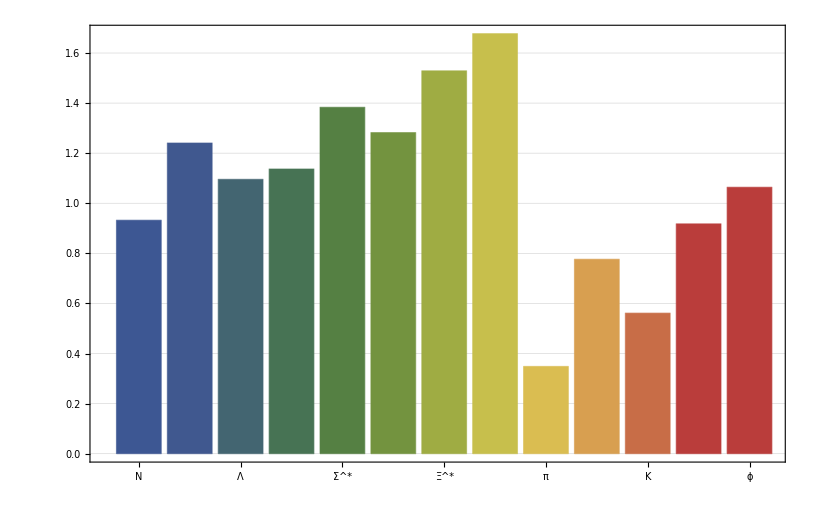

{My Error}

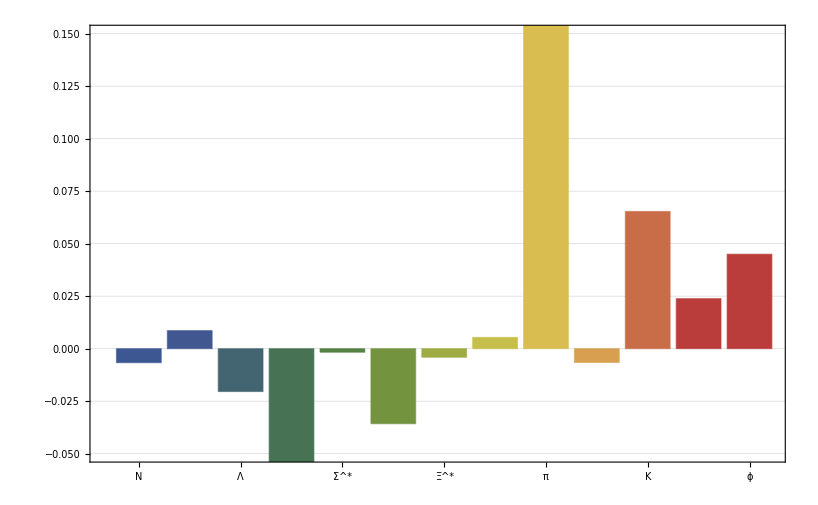

{MIT's Error}

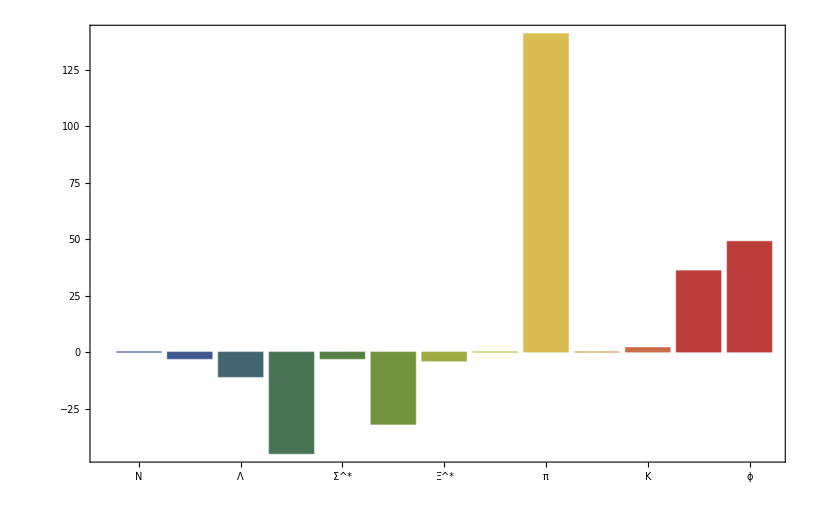

{Charge Radius}

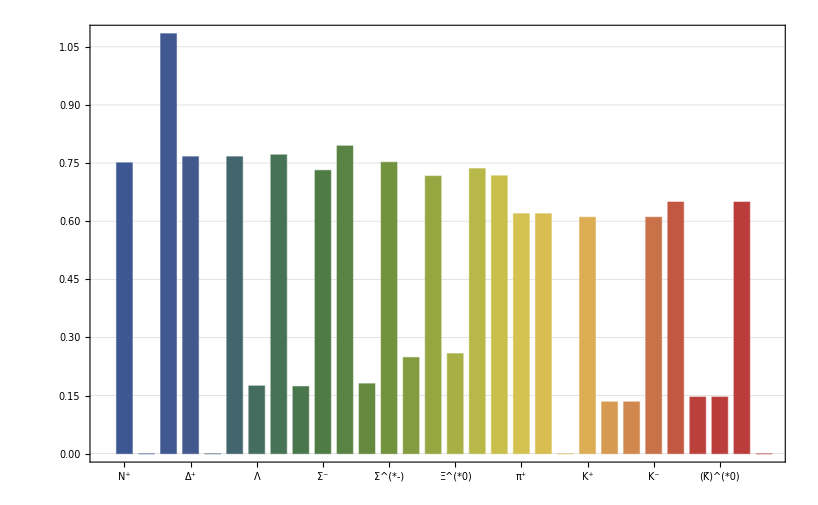

{Magnetic Moment}

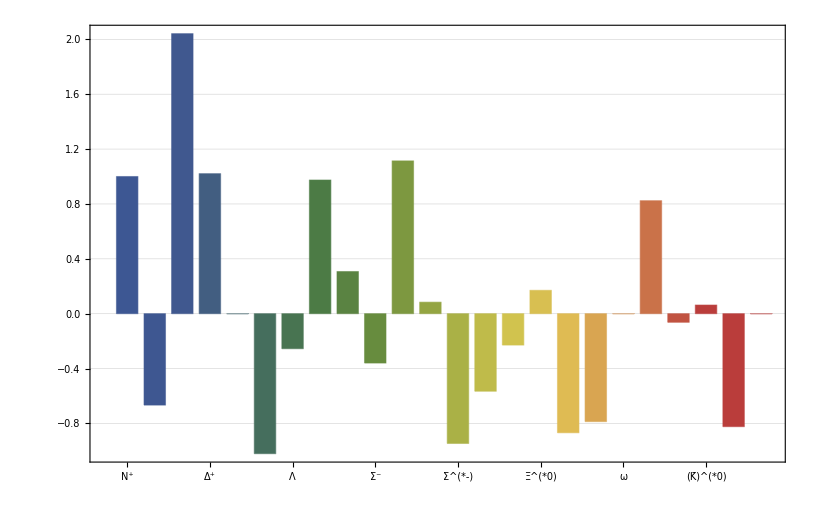

```mathematica
<<MITBagModel\MITBagModel.m

{"N 1/2+ 0.939"}
Nc=Hadron[{0,0,0,3},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}},0]
rNp=ChargeRadius[{0,0,0,2,1},{0,0,0,0,0},Nc];
rN0=ChargeRadius[{0,0,0,1,2},{0,0,0,0,0},Nc];
μNp=MagneticMoment[{0,0,0,4/3,-1/3},{0,0,0,0,0},Nc];
μN0=MagneticMoment[{0,0,0,-1/3,4/3},{0,0,0,0,0},Nc];
{rNp,rN0}
{{μNp,μN0},{μNp/μNp,μN0/μNp}}

{"Δ 3/2+ 1.232"}
Δ=Hadron[{0,0,0,3},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-8}},0]
rΔpp=ChargeRadius[{0,0,0,3,0},{0,0,0,0,0},Δ];
rΔp=ChargeRadius[{0,0,0,2,1},{0,0,0,0,0},Δ];
rΔ0=ChargeRadius[{0,0,0,1,2},{0,0,0,0,0},Δ];
rΔm=ChargeRadius[{0,0,0,0,3},{0,0,0,0,0},Δ];
μΔpp=MagneticMoment[{0,0,0,3,0},{0,0,0,0,0},Δ];
μΔp=MagneticMoment[{0,0,0,2,1},{0,0,0,0,0},Δ];
μΔ0=MagneticMoment[{0,0,0,1,2},{0,0,0,0,0},Δ];
μΔm=MagneticMoment[{0,0,0,0,3},{0,0,0,0,0},Δ];
{rΔpp,rΔp,rΔ0,rΔm}
{{μΔpp,μΔp,μΔ0,μΔm},{μΔpp/μNp,μΔp/μNp,μΔ0/μNp,μΔm/μNp}}

{"Λ 1/2+ 1.116"}
Λ=Hadron[{0,0,1,2},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}},0]
rΛ=ChargeRadius[{0,0,1,1,1},{0,0,0,0,0},Λ];
μΛ=MagneticMoment[{0,0,1,0,0},{0,0,0,0,0},Λ];
{rΛ}
{{μΛ},{μΛ/μNp}}

{"Σ 1/2+ 1.193"}
Σ=Hadron[{0,0,1,2},{{0,0,0,0},{0,0,0,0},{0,0,0,32/3},{0,0,0,-8/3}},0]
rΣp=ChargeRadius[{0,0,1,2,0},{0,0,0,0,0},Σ];
rΣ0=ChargeRadius[{0,0,1,1,1},{0,0,0,0,0},Σ];
rΣm=ChargeRadius[{0,0,1,0,2},{0,0,0,0,0},Σ];
μΣp=MagneticMoment[{0,0,-1/3,4/3,0},{0,0,0,0,0},Σ];μΣ0=MagneticMoment[{0,0,-1/3,2/3,2/3},{0,0,0,0,0},Σ];μΣm=MagneticMoment[{0,0,-1/3,0,4/3},{0,0,0,0,0},Σ];
{rΣp,rΣ0,rΣm}
{{μΣp,μΣ0,μΣm},{μΣp/μNp,μΣ0/μNp,μΣm/μNp}}

{"Σ^* 3/2+ 1.385"}
SuperStar[Σ]=Hadron[{0,0,1,2},{{0,0,0,0},{0,0,0,0},{0,0,0,-16/3},{0,0,0,-8/3}},0]
SuperStar[rΣp]=ChargeRadius[{0,0,1,2,0},{0,0,0,0,0},SuperStar[Σ]];
SuperStar[rΣ0]=ChargeRadius[{0,0,1,1,1},{0,0,0,0,0},SuperStar[Σ]];
SuperStar[rΣm]=ChargeRadius[{0,0,1,0,2},{0,0,0,0,0},SuperStar[Σ]];
SuperStar[μΣp]=MagneticMoment[{0,0,1,2,0},{0,0,0,0,0},SuperStar[Σ]];
SuperStar[μΣ0]=MagneticMoment[{0,0,1,1,1},{0,0,0,0,0},SuperStar[Σ]];
SuperStar[μΣm]=MagneticMoment[{0,0,1,0,2},{0,0,0,0,0},SuperStar[Σ]];
{SuperStar[rΣp],SuperStar[rΣ0],SuperStar[rΣm]}
{{SuperStar[μΣp],SuperStar[μΣ0],SuperStar[μΣm]},{SuperStar[μΣp]/μNp,SuperStar[μΣ0]/μNp,SuperStar[μΣm]/μNp}}

{"Ξ 1/2+ 1.318"}
Ξ=Hadron[{0,0,2,1},{{0,0,0,0},{0,0,0,0},{0,0,-8/3,32/3},{0,0,0,0}},0]
rΞ0=ChargeRadius[{0,0,2,1,0},{0,0,0,0,0},Ξ];
rΞm=ChargeRadius[{0,0,2,0,1},{0,0,0,0,0},Ξ];
μΞ0=MagneticMoment[{0,0,4/3,-1/3,0},{0,0,0,0,0},Ξ];
μΞm=MagneticMoment[{0,0,4/3,0,-1/3},{0,0,0,0,0},Ξ];
{rΞ0,rΞm}
{{μΞ0,μΞm},{μΞ0/μNp,μΞm/μNp}}

{"Ξ^* 3/2+ 1.533"}
SuperStar[Ξ]=Hadron[{0,0,2,1},{{0,0,0,0},{0,0,0,0},{0,0,-8/3,-16/3},{0,0,0,0}},0]
SuperStar[rΞ0]=ChargeRadius[{0,0,2,1,0},{0,0,0,0,0},SuperStar[Ξ]];
SuperStar[rΞm]=ChargeRadius[{0,0,2,0,1},{0,0,0,0,0},SuperStar[Ξ]];
SuperStar[μΞ0]=MagneticMoment[{0,0,2,1,0},{0,0,0,0,0},SuperStar[Ξ]];
SuperStar[μΞm]=MagneticMoment[{0,0,2,0,1},{0,0,0,0,0},SuperStar[Ξ]];
{SuperStar[rΞ0],SuperStar[rΞm]}
{{SuperStar[μΞ0],SuperStar[μΞm]},{SuperStar[μΞ0]/μNp,SuperStar[μΞm]/μNp}}

{"Ω 3/2+ 1.672"}
Ω=Hadron[{0,0,3,0},{{0,0,0,0},{0,0,0,0},{0,0,-8,0},{0,0,0,0}},0]
rΩ=ChargeRadius[{0,0,3,0,0},{0,0,0,0,0},Ω];
μΩ=MagneticMoment[{0,0,3,0,0},{0,0,0,0,0},Ω];
{rΩ}
{{μΩ},{μΩ/μNp}}

{"π 0- 0.137"}
π0=Hadron[{0,0,0,2},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,16}},0]
rπp=ChargeRadius[{0,0,0,1,0},{0,0,0,0,1},π0];
rπm=ChargeRadius[{0,0,0,0,1},{0,0,0,1,0},π0];
{rπp,rπm}

{"ω 1- 0.783"}
ω0=Hadron[{0,0,0,2},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-16/3}},0]
rω0=ChargeRadius[{0,0,0,1,0},{0,0,0,1,0},ω0];
μω0=MagneticMoment[{0,0,0,1,0},{0,0,0,1,0},ω0];
{rω0}
{{μω0},{μω0/μNp}}

{"K 0- 0.496"}
K=Hadron[{0,0,1,1},{{0,0,0,0},{0,0,0,0},{0,0,0,16},{0,0,0,0}},0]
rKp=ChargeRadius[{0,0,0,1,0},{0,0,1,0,0},K];
rK0=ChargeRadius[{0,0,0,0,1},{0,0,1,0,0},K];
rK0bar=ChargeRadius[{0,0,1,0,0},{0,0,0,0,1},K];
rKm=ChargeRadius[{0,0,1,0,0},{0,0,0,1,0},K];
{rKp,rK0,rK0bar,rKm}

{"K^* 1- 0.894"}
SuperStar[K]=Hadron[{0,0,1,1},{{0,0,0,0},{0,0,0,0},{0,0,0,-16/3},{0,0,0,0}},0]
SuperStar[rKp]=ChargeRadius[{0,0,0,1,0},{0,0,1,0,0},SuperStar[K]];
SuperStar[rK0]=ChargeRadius[{0,0,0,0,1},{0,0,1,0,0},SuperStar[K]];
SuperStar[rK0bar]=ChargeRadius[{0,0,1,0,0},{0,0,0,0,1},SuperStar[K]];
SuperStar[rKm]=ChargeRadius[{0,0,1,0,0},{0,0,0,1,0},SuperStar[K]];
SuperStar[μKp]=MagneticMoment[{0,0,0,1,0},{0,0,1,0,0},SuperStar[K]];
SuperStar[μK0]=MagneticMoment[{0,0,0,0,1},{0,0,1,0,0},SuperStar[K]];
SuperStar[μK0bar]=MagneticMoment[{0,0,1,0,0},{0,0,0,0,1},SuperStar[K]];
SuperStar[μKm]=MagneticMoment[{0,0,1,0,0},{0,0,0,1,0},SuperStar[K]];
{SuperStar[rKp],SuperStar[rK0],SuperStar[rK0bar],SuperStar[rKm]}
{{SuperStar[μKp],SuperStar[μK0],SuperStar[μK0bar],SuperStar[μKm]},{SuperStar[μKp]/μNp,SuperStar[μK0]/μNp,SuperStar[μK0bar]/μNp,SuperStar[μKm]/μNp}}

{"ϕ 1- 1.019"}
ϕ=Hadron[{0,0,2,0},{{0,0,0,0},{0,0,0,0},{0,0,-16/3,0},{0,0,0,0}},0]
rϕ=ChargeRadius[{0,0,1,0,0},{0,0,1,0,0},ϕ];
μϕ=MagneticMoment[{0,0,1,0,0},{0,0,1,0,0},ϕ];
{rϕ}
{{μϕ},{μϕ/μNp}}

{"Mass Spectrum"}
BarChart[{First[Nc],First[Δ],First[Λ],First[Σ],First[SuperStar[Σ]],First[Ξ],First[SuperStar[Ξ]],First[Ω],First[π0],First[ω0],First[K],First[SuperStar[K]],First[ϕ]},Frame->True,ChartLabels->{"N","Δ","Λ","Σ","Σ^*","Ξ","Ξ^*","Ω","π","ω","K","K^*","ϕ"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"My Error"}
BarChart[{(First[Nc]-0.939),
(First[Δ]-1.232),
(First[Λ]-1.116),
(First[Σ]-1.193),
(First[SuperStar[Σ]]-1.385),
(First[Ξ]-1.318),
(First[SuperStar[Ξ]]-1.533),
(First[Ω]-1.672),
(First[π0]-0.137),
(First[ω0]-0.783),
(First[K]-0.496),
(First[SuperStar[K]]-0.894),
(First[ϕ]-1.019)},Frame->True,ChartLabels->{"N","Δ","Λ","Σ","Σ^*","Ξ","Ξ^*","Ω","π","ω","K","K^*","ϕ"},ChartStyle->"DarkRainbow",PlotRange->{-0.05,0.150},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"MIT's Error"}
BarChart[{0,-3,-11,-45,-3,-32,-4,0,141,0,2,36,49},Frame->True,ChartLabels->{"N","Δ","Λ","Σ","Σ^*","Ξ","Ξ^*","Ω","π","ω","K","K^*","ϕ"},ChartStyle->"DarkRainbow"]

{"Charge Radius"}
BarChart[{rNp,rN0,rΔpp,rΔp,rΔ0,rΔm,rΛ,rΣp,rΣ0,rΣm,SuperStar[rΣp],SuperStar[rΣ0],SuperStar[rΣm],rΞ0,rΞm,SuperStar[rΞ0],SuperStar[rΞm],rΩ,rπp,rπm,rω0,rKp,rK0,rK0bar,rKm,SuperStar[rKp],SuperStar[rK0],SuperStar[rK0bar],SuperStar[rKm],rϕ},Frame->True,ChartLabels->{"N^+","N^0","Δ^(++)","Δ^+","Δ^0","Δ^-","Λ","Σ^+","Σ^0","Σ^-","Σ^(*+)","Σ^(*0)","Σ^(*-)","Ξ^0","Ξ^-","Ξ^(*0)","Ξ^(*-)","Ω","π^+","π^-","ω","K^+","K^0","(K̄)^0","K^-","K^(*+)","K^(*0)","(K̄)^(*0)","K^(*-)","ϕ"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Magnetic Moment"}
BarChart[{μNp/μNp,μN0/μNp,μΔpp/μNp,μΔp/μNp,μΔ0/μNp,μΔm/μNp,μΛ/μNp,μΣp/μNp,μΣ0/μNp,μΣm/μNp,SuperStar[μΣp]/μNp,SuperStar[μΣ0]/μNp,SuperStar[μΣm]/μNp,μΞ0/μNp,μΞm/μNp,SuperStar[μΞ0]/μNp,SuperStar[μΞm]/μNp,μΩ/μNp,μω0/μNp,SuperStar[μKp]/μNp,SuperStar[μK0]/μNp,SuperStar[μK0bar]/μNp,SuperStar[μKm]/μNp,μϕ/μNp},Frame->True,ChartLabels->{"N^+","N^0","Δ^(++)","Δ^+","Δ^0","Δ^-","Λ","Σ^+","Σ^0","Σ^-","Σ^(*+)","Σ^(*0)","Σ^(*-)","Ξ^0","Ξ^-","Ξ^(*0)","Ξ^(*-)","Ω","ω","K^(*+)","K^(*0)","(K̄)^(*0)","K^(*-)","ϕ"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]
```